## Load Lib

```mathematica
AppendTo[$Path,"C:\\Users\\hp\\Desktop\\Wolfram Summer School\\project\\Tile\\GeneralTile"];
Get["HappyTile.wl"]
```

# First Phase

This Phase is to use Points representing angle and intersection test to generate and filter cases.

## Functions

### Tiles Polygons

```mathematica
H2poly=;
H1poly=;
```

```mathematica
H8poly=Polygon[];
H7poly=Polygon[];
```

```mathematica
AH7superPoly=;
H8superPoly=;
```

```mathematica
metaTile[pos_,dir_:0,pt_,choice_:True]:=With[{
vertices=If[
TrueQ[choice],
RotationMatrix[dir*Pi/6].#&/@,
RotationMatrix[dir*Pi/6].#&/@
]
},
Polygon[vertices+Threaded[pos-vertices[[pt]]]]
]
```

```mathematica
cluster[pos_,dir_:0,pt_,choice_:False]:=With[{
vertices=If[
TrueQ[choice],
RotationMatrix[dir*Pi/6].#&/@,
RotationMatrix[dir*Pi/6].#&/@
]
},
Polygon[vertices+Threaded[pos-vertices[[pt]]]]
]
```

```mathematica
clusterSuper1[pos_,dir_:0,pt_,choice_:False]:=With[{
vertices=If[
TrueQ[choice],
RotationMatrix[dir*Pi/6].#&/@,
RotationMatrix[dir*Pi/6].#&/@
]
},
Polygon[vertices+Threaded[pos-vertices[[pt]]]]
]
```

```mathematica
angleVertices[angle_][poly_]:=First/@Position[PolygonAngle[poly],_?(#==2Pi*angle&),{1}]
```

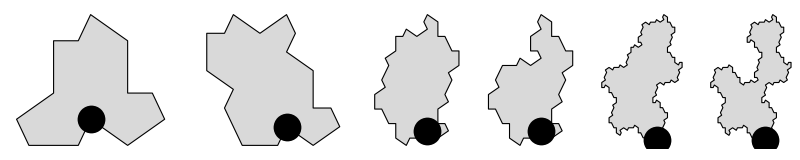

```mathematica
Graphics[
{
LightGray,
EdgeForm[Black],
#,
Black,PointSize[.05],
Point[First[#][[1]]]
}
]&/@{H1poly,H2poly,H8poly,H7poly,H8superPoly,AH7superPoly}//GraphicsRow[#,ImageSize->800]&
```

```mathematica
angleToPointsBuildFunction=Function[
{choice,tileFunction},
angleToPoints[ToString[tileFunction]][choice]=Association[#->Join@@Position[
RegionMember[
tileFunction[{0,0},0,1,choice],
CirclePoints[First[tileFunction[{0,0},0,1,choice]][[#]],{1/4,Pi/12},12]
],True
]&/@Range[Length[First[tileFunction[{0,0},0,1,choice]]]]]
];
```

### Project Tiles Code

```mathematica
metaTileCode[pos_,dir_:0,pt_,False]:=With[{
vertices=
},
{pos+RotationMatrix[dir*Pi/6].(#1-vertices[[pt]]),Mod[#2+If[TrueQ[#3],-dir,dir],12],#3,#4}&@@@
]
```

```mathematica
metaTileCode[pos_,dir_:0,pt_,True]:=With[{
vertices=
},
{pos+RotationMatrix[dir*Pi/6].(#1-vertices[[pt]]),Mod[#2+If[TrueQ[#3],-dir,dir],12],#3,#4}&@@@{{{0,0},0,False,1}}
]
```

```mathematica
clusterCode[pos_,dir_,pt_,False]:=With[
{H7vertices=},
	{
		pos+RotationMatrix[dir Pi/6].(#1-H7vertices[[pt]]),
		Mod[If[TrueQ[#3],-dir,dir]+#2,12],
		#3,#4
	}&@@@
];
```

```mathematica
clusterCode[pos_,dir_,pt_,True]:=With[
{H8vertices=},
	{
		pos+RotationMatrix[dir Pi/6].(#1-H8vertices[[pt]]),
		Mod[If[TrueQ[#3],-dir,dir]+#2,12],
		#3,#4
	}&@@@
];
```

### angle information

```mathematica
angleToPoints["metaTile"][True]=;
angleToPoints["metaTile"][False]=;
```

```mathematica
angleToPoints["cluster"][True]=;
angleToPoints["cluster"][False]=;
```

```mathematica
angleToPoints["clusterSuper1"][True]=;
angleToPoints["clusterSuper1"][False]=;
```

```mathematica
getPointsOccupation[tileFunction_][dir_,pt_,choice_]:=Mod[#+dir,12,1]&/@(pt/.angleToPoints[ToString[tileFunction]][choice])
```

### intersectingQ

```mathematica
intersectingQ[p1_Polygon,p2_Polygon,dimension_Integer:10]:=With[{res=PlanarPolygonFragmentation[p1,p2,dimension]},If[res==={}||Total[Length/@res]==3,False,True]]
intersectingQ[ps_List,dimension_Integer:10]:=Fold[
If[
#1===False,
False,
With[{res=PlanarPolygonFragmentation[#1,#2,dimension]},
If[Total[Length/@res]==3,SortBy[res,Length][[1,1]],False]
]
]&,
ps
]
```

### all rotations

```mathematica
allRotations=Function[r,Sort[Apply[{Mod[#1+r,12],#2,#3}&,#,{1}]]]/@Range[0,11]&;
```

## Meta-tile

```mathematica
allcases=Join@@(Tuples[{
Range[0,11],
Range[Length[First[metaTile[{0,0},0,1,#]]]],
{#}
}]&/@{False,True});
allcases//Length
```

408

```mathematica
pointsToCases=GroupBy[allcases,Sort[getPointsOccupation[metaTile]@@#]&];
```

```mathematica
cases=Tuples[{
pointsToCases[{1,2,3,4}],
pointsToCases[{5,6,7,8}],
pointsToCases[{9,10,11,12}]
}];
cases//Length
```

2197

```mathematica
rotationFreeCases=DeleteDuplicatesBy[Sort@*allRotations][cases];
rotationFreeCases//Length
```

741

```mathematica
Timing[res1=Select[
rotationFreeCases,
intersectingQ[metaTile[{0,0},##]&@@@#,10]=!=False&
];]
```

{42.1094,Null}

```mathematica
res1//Length
```

34

```mathematica
Iconize[res1]
```

Show result:

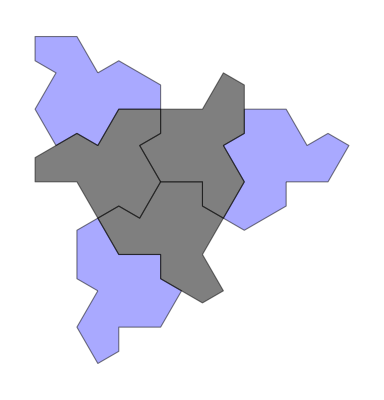
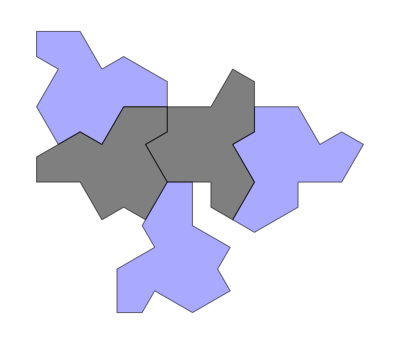
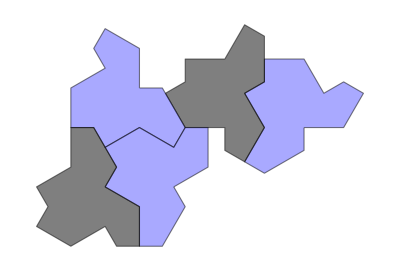
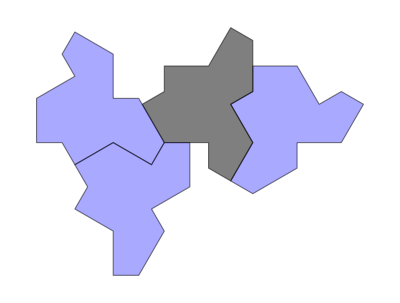
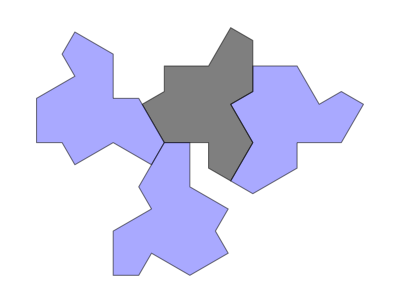
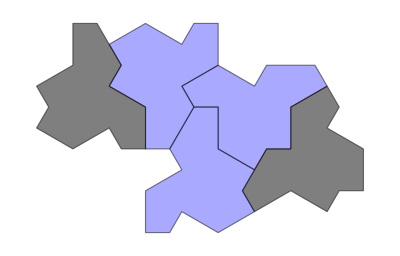
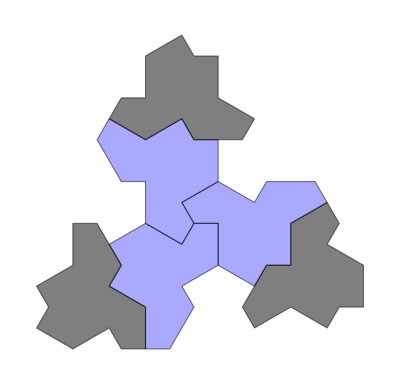
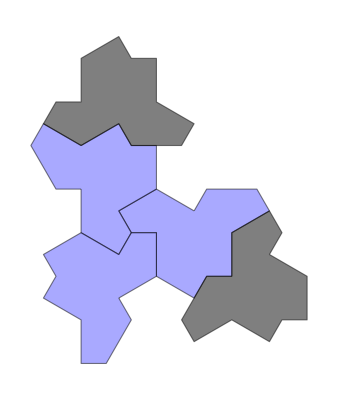
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Partition[show[metaTileCode[{0,0},##]&@@@#]&/@res1,UpTo[7]]//Grid[#,Frame->All,FrameStyle->LightGray]&
```

Every one including reflected tile seem invalid. Since we know every reflected tile force a H8 from result before, we can do replacement here.

```mathematica
transformCode[vec_,r_][code_]:={vec+RotationMatrix[r*Pi/6].#1,Mod[#2+If[TrueQ[#3],-r,r],12],#3,#4}&@@@code;
```

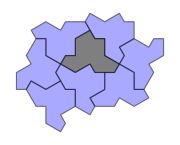

```mathematica
transformCode[#1,Mod[-#2,12]][]&@@{{0,0},0,1,True}//show[#,ImageSize->Small]&
```

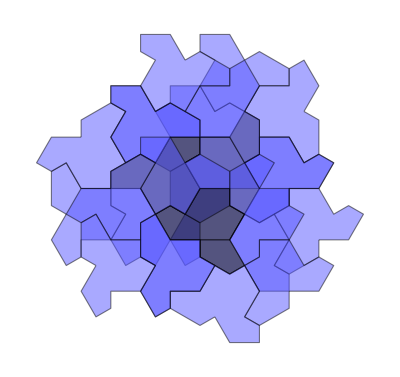
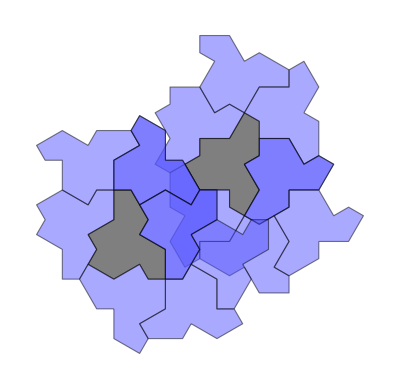
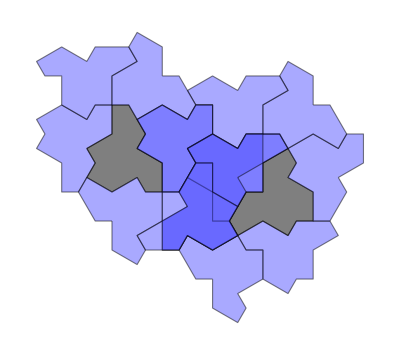
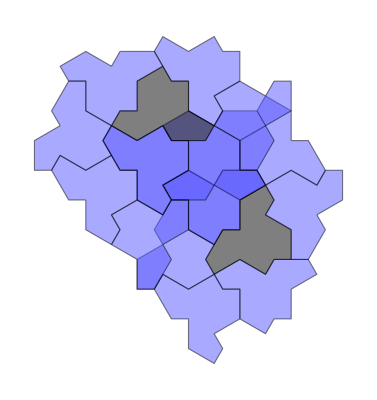
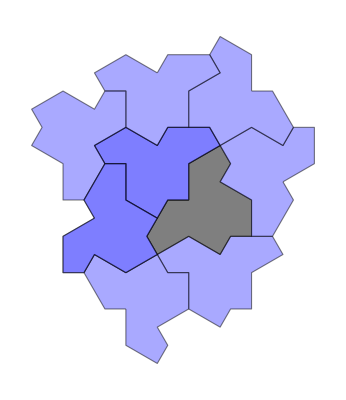
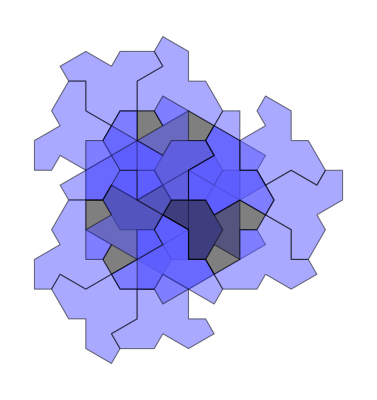
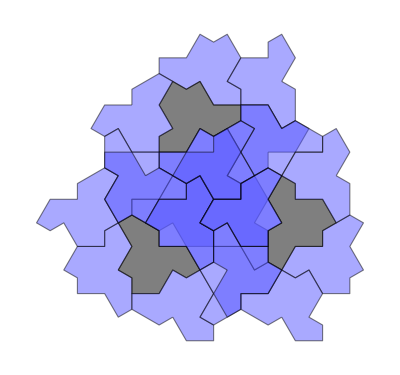

```mathematica
show/@Replace[
Map[Sequence@@metaTileCode[{0,0},Sequence@@#]&,res1,{2}],tile_/;TrueQ[tile[[3]]]:>Sequence@@((transformCode[First[hatVertices@@tile],Mod[-tile[[2]],12]][])),
{2}][[{1,3,6,8,10,15,18}]]//Row
```

```mathematica
MapIndexed[Labeled[show[#1],First[#2]]&,Replace[
Map[Sequence@@metaTileCode[{0,0},Sequence@@#]&,res1,{2}],tile_/;TrueQ[tile[[3]]]:>Sequence@@((transformCode[First[hatVertices@@tile],Mod[-tile[[2]],12]][])),
{2}]]
```

Then, we can know who are true positive.

```mathematica
res2=Join[res1[[{10,14,23,24}]],res1[[25;;]]];
```

```mathematica
show/@Map[Sequence@@metaTileCode[{0,0},Sequence@@#]&,res2,{2}]//{{Sequence@@#[[;;4]]},#[[5;;]]}&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

The second row is 10 1/3 Vertex theorem before. {12,12,12} and {6,6,6} show up. They are invalid, prove in https://community.wolfram.com/groups/-/m/t/2967510?p_p_auth=TA87VcJx.

```mathematica
Iconize[res2]
```

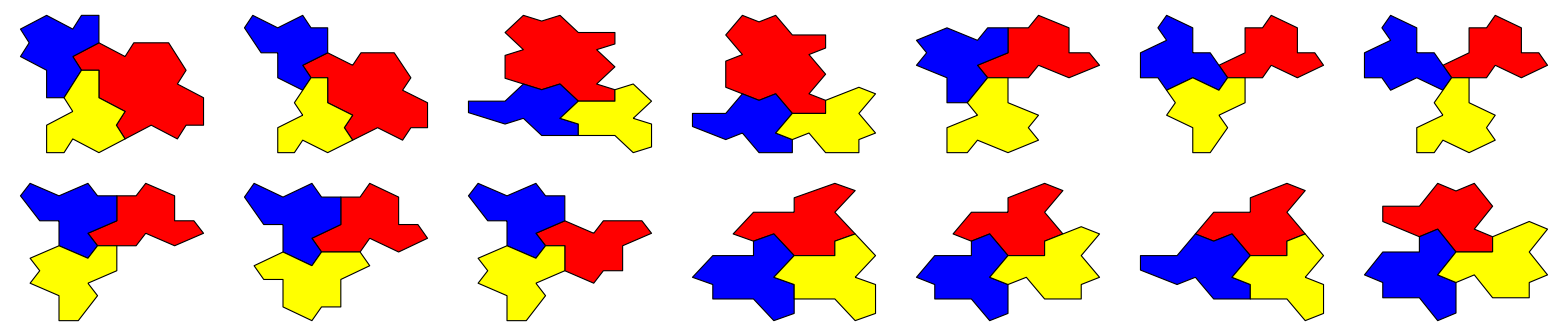

```mathematica
(Graphics[{EdgeForm[Black],Red,#1,Blue,#2,Yellow,#3}]&@@(metaTile[{0,0},Sequence@@#]&/@#))&/@res2//Partition[#,UpTo[7]]&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

## 0-super-tile

```mathematica
vertexClass[True]=Association@Flatten[Function[n,
#->n&/@Flatten[
Position[First[cluster[{0,0},10,1,True]],Alternatives@@((hatVertices@@#)[[n]]&/@)]
]
]/@Range[14]];
vertexClass[False]=Association@Flatten[Function[n,
#->n&/@Flatten[
Position[First[cluster[{0,0},10,1,False]],Alternatives@@((hatVertices@@#)[[n]]&/@)]
]
]/@Range[14]];
```

```mathematica
validVF=oneThirdVertexTheoremLis[{1,Sqrt[3]}][[All,All,3]]
```

{{12,12,14},{4,12,14},{4,12,12},{4,4,12},{4,4,4},{2,6,6},{2,2,6},{2,2,2}}

```mathematica
allStatesForOne=Join@@(Tuples[{Range[0,11],angleVertices[1/3][cluster[{0,0},0,1,#]],{#}}]&/@{True,False});
allStatesForOne//Length
```

312

```mathematica
classifiedByVertexAndPoints=GroupBy[
allStatesForOne,
{#[[2]]/.Join[vertexClass[False],vertexClass[True]],Sort[getPointsOccupation[cluster]@@#]}&
];
```

```mathematica
cases=Join@@(Tuples[{
classifiedByVertexAndPoints[{#1,{1,2,3,4}}],
classifiedByVertexAndPoints[{#2,{5,6,7,8}}],
classifiedByVertexAndPoints[{#3,{9,10,11,12}}]
}]&@@@validVF);
cases//Length
```

1330

```mathematica
rotationFreeCases=DeleteDuplicatesBy[Sort@*allRotations][cases];
rotationFreeCases//Length
```

630

```mathematica
Timing[res3=Select[
rotationFreeCases,
intersectingQ[cluster[{0,0},##]&@@@#,15]=!=False&
];]
```

{102.969,Null}

```mathematica
res3//Length
```

69

This is 15 1/3V for H8.

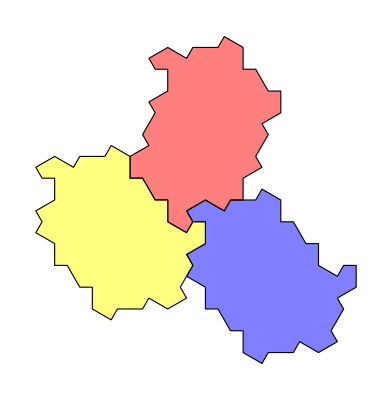
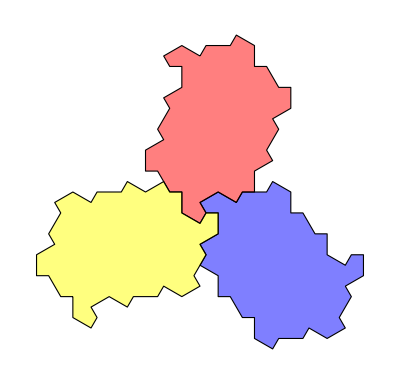
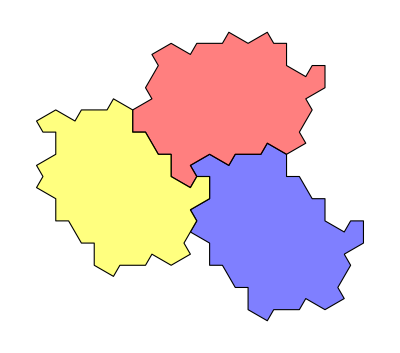
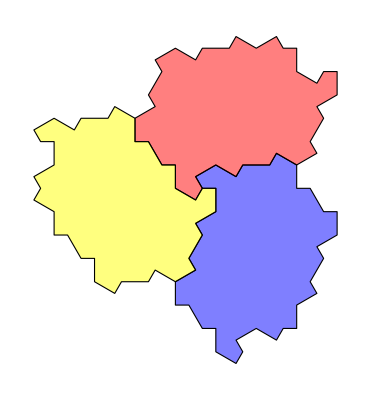
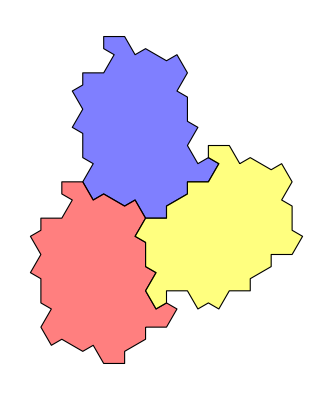
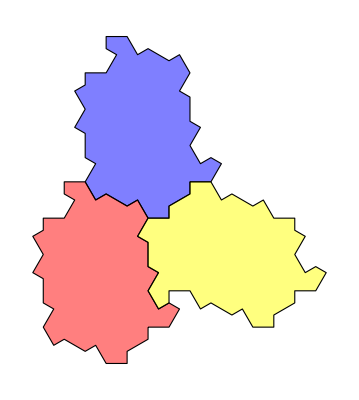
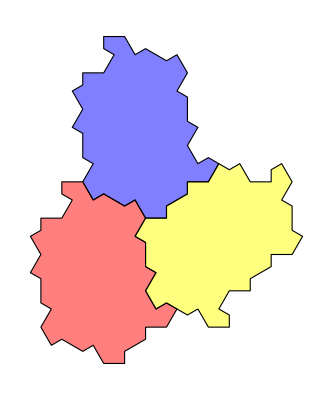
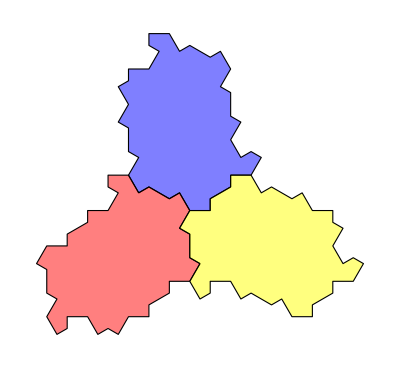
-Graphics-{4,True}
{20,True}
{20,True} | -Graphics-{20,True}
{20,True}
{20,True} | -Graphics-{4,True}
{4,True}
{20,True} | -Graphics-{4,True}
{4,True}
{4,True} | -Graphics-{12,True}
{12,True}
{38,True}
-Graphics-{12,True}
{38,True}
{38,True} | -Graphics-{12,True}
{32,True}
{38,True} | -Graphics-{38,True}
{38,True}
{38,True} | -Graphics-{32,True}
{38,True}
{38,True} | -Graphics-{12,True}
{32,True}
{38,True}
-Graphics-{32,True}
{32,True}
{38,True} | -Graphics-{12,True}
{12,True}
{32,True} | -Graphics-{12,True}
{32,True}
{32,True} | -Graphics-{32,True}
{32,True}
{32,True} | -Graphics-{12,True}
{12,True}
{12,True}

```mathematica
Partition[
Labeled[
Graphics[
{
EdgeForm[Black],
Opacity[0.5],
Blue,
cluster[{0,0},##]&@@#1,
Red,
cluster[{0,0},##]&@@#2,
Yellow,
cluster[{0,0},##]&@@#3
}],Column[Sort[{##}[[All,{2,3}]]]]]&@@@Select[res3,FreeQ[False]],UpTo[5]]//Grid[#,Frame->All,FrameStyle->LightGray]&
```

With H7. If H7 use its 18 or 20 vertex to form the v.f, it must form H8.

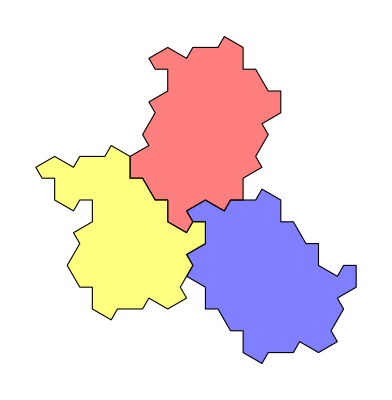
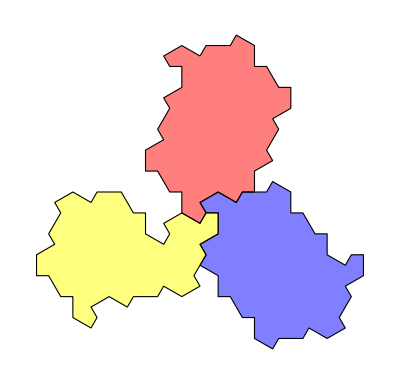
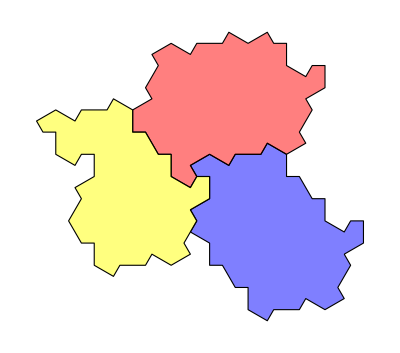
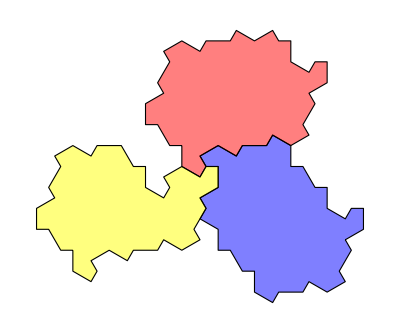
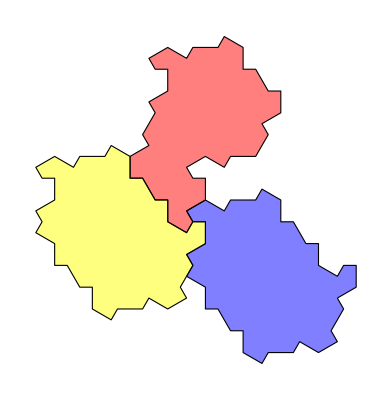
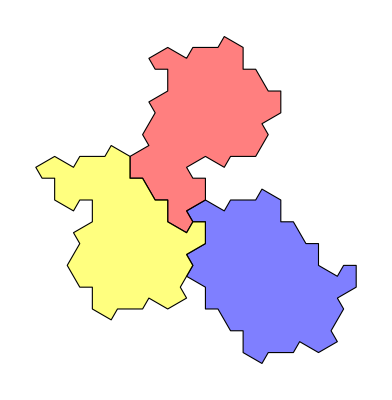
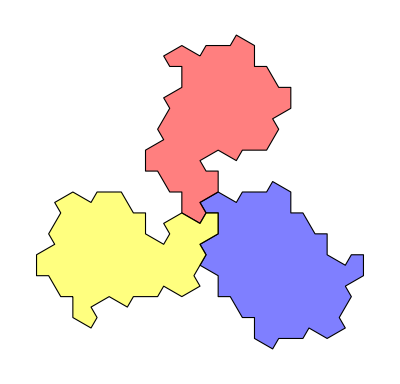
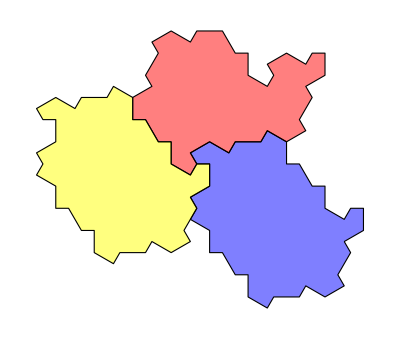
-Graphics-{4,False}
{20,True}
{20,True} | -Graphics-{20,False}
{20,True}
{20,True} | -Graphics-{4,False}
{4,True}
{20,True} | -Graphics-{4,True}
{20,False}
{20,True} | -Graphics-{4,True}
{20,False}
{20,True} | -Graphics-{4,False}
{20,False}
{20,True} | -Graphics-{20,False}
{20,False}
{20,True} | -Graphics-{4,False}
{4,True}
{20,True} | -Graphics-{4,False}
{4,False}
{20,True} | -Graphics-{4,False}
{20,False}
{20,True}
-Graphics-{4,False}
{4,True}
{4,True} | -Graphics-{4,True}
{4,True}
{20,False} | -Graphics-{4,False}
{4,True}
{20,False} | -Graphics-{4,True}
{20,False}
{20,False} | -Graphics-{4,False}
{4,False}
{4,True} | -Graphics-{4,False}
{4,True}
{20,False} | -Graphics-{4,False}
{20,False}
{20,False} | -Graphics-{20,False}
{20,False}
{20,False} | -Graphics-{4,False}
{4,False}
{20,False} | -Graphics-{4,False}
{4,False}
{4,False}
-Graphics-{12,True}
{18,False}
{38,True} | -Graphics-{12,False}
{12,True}
{38,True} | -Graphics-{18,False}
{38,True}
{38,True} | -Graphics-{12,False}
{38,True}
{38,True} | -Graphics-{18,False}
{32,True}
{38,True} | -Graphics-{12,False}
{32,True}
{38,True} | -Graphics-{12,False}
{12,True}
{38,True} | -Graphics-{12,False}
{32,True}
{38,True} | -Graphics-{12,False}
{18,False}
{38,True} | -Graphics-{12,False}
{12,False}
{38,True}
-Graphics-{12,True}
{18,False}
{38,True} | -Graphics-{18,False}
{32,True}
{38,True} | -Graphics-{18,False}
{18,False}
{38,True} | -Graphics-{12,False}
{18,False}
{38,True} | -Graphics-{12,True}
{18,False}
{32,True} | -Graphics-{12,False}
{12,True}
{32,True} | -Graphics-{18,False}
{32,True}
{32,True} | -Graphics-{12,False}
{32,True}
{32,True} | -Graphics-{12,False}
{12,True}
{32,True} | -Graphics-{12,False}
{18,False}
{32,True}
-Graphics-{12,False}
{12,False}
{32,True} | -Graphics-{12,True}
{18,False}
{32,True} | -Graphics-{18,False}
{18,False}
{32,True} | -Graphics-{12,False}
{18,False}
{32,True} | -Graphics-{12,True}
{12,True}
{18,False} | -Graphics-{12,False}
{12,True}
{12,True} | -Graphics-{12,False}
{12,True}
{18,False} | -Graphics-{12,False}
{12,False}
{12,True} | -Graphics-{12,True}
{18,False}
{18,False} | -Graphics-{12,False}
{12,True}
{18,False}
-Graphics-{12,False}
{18,False}
{18,False} | -Graphics-{12,False}
{12,False}
{18,False} | -Graphics-{18,False}
{18,False}
{18,False} | -Graphics-{12,False}
{12,False}
{12,False} |  |  |  |  |  |

```mathematica
Partition[
Labeled[
Graphics[
{
EdgeForm[Black],
Opacity[0.5],
Blue,
cluster[{0,0},##]&@@#1,
Red,
cluster[{0,0},##]&@@#2,
Yellow,
cluster[{0,0},##]&@@#3
}],Column[Sort[{##}[[All,{2,3}]]]]]&@@@Select[res3,!FreeQ[#,False]&],UpTo[10]]//Grid[#,Frame->All,FrameStyle->LightGray]&
```

```mathematica
Iconize[res3]
```

# Second Phase ( Unused)

This phase is to eliminate as much 15 1/3 v.f. for H8 before as possible. In fact, the result should be only 8 left as hat tile.

## Color Rule

```mathematica
colorRules = MapThread[Rule,
{
	{
		{12,12,14},
		{4,12,14},
		{4,12,12},
		{4,4,12},
		{4,4,4},
		{2,6,6},
		{2,2,6},
		{2,2,2}
	},
	Hue/@Range[1/9,8/9,1/9]
}
];
```

## Graph Function

```mathematica
depthNode[n_][g_] :=With[{root=First[VertexList[g]]},Select[VertexList[g],(GraphDistance[g,root,#]===n&)]];
```

```mathematica
leaves=ResourceFunction["DepthFirstSearch"][#,First@VertexList[#],(True&),All]&;
```

```mathematica
vertexConfigurationFind[vertexConf_List:oneThirdVertexTheoremLis[{1,Sqrt[3]}][[All,All,3]]][state_Association]:=
Association[Function[conf,
conf->Keys[Select[getVerticesInf[state["code"]][[All,All,1]],MatchQ[#,{OrderlessPatternSequence@@conf}]&]]
]/@vertexConf]
```

```mathematica
vertexConfigurationFind[vertexConf_List:oneThirdVertexTheoremLis[{1,Sqrt[3]}][[All,All,3]]][code_List]:=
Association[Function[conf,
conf->Keys[Select[getVerticesInf[code][[All,All,1]],MatchQ[#,{OrderlessPatternSequence@@conf}]&]]
]/@vertexConf]
```

```mathematica
formatGraph[g_,opt:OptionsPattern[Graph]]:=Graph[g,
opt,
GraphLayout->"LayeredDigraphEmbedding",
VertexShapeFunction->(
Inset[
Show[
{
show[#2["code"],EdgeForm->Gray,ChooseColor->{Lighter@LightGray,Darker@Gray}],
Graphics[
{
PointSize[0.03],
KeyValueMap[
If[#2=!={},{#1/.colorRules,Point[#2]},Nothing]&,
vertexConfigurationFind[][#2]
]
}
]
}
],
#1,Center,8*#3
]&
),
EdgeShapeFunction -> ({Red,Arrowheads[0.005],Arrow[#1, 0.1]}&)
]
```

## Vertex Number Convention

First vertex position shown as black vertex, and continue to number counter-clockwise.

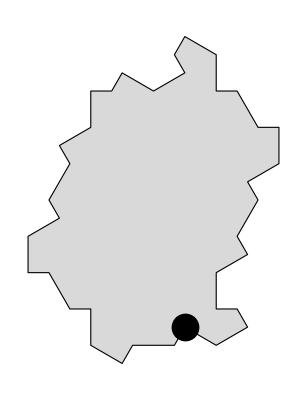
{-Graphics-,-Graphics-}

```mathematica
Graphics[
{
LightGray,
EdgeForm[Black],
#,
Black,PointSize[.05],
Point[First[#][[1]]]
}
]&/@{Polygon[],Polygon[]}
```

Notice: every hat tile are numbered as 14 vertices rule, which means each edge with length 2 is made up with two edges with length 1 and a 1/2 vertex.

## 1/3 Vertex Configuration Result of 1st Phase

```mathematica
resultofFirstPhase=;
```

```mathematica
firstPhaseResultCode=Join@@(clusterCode[{0,0},Sequence@@#]&/@#)&/@resultofFirstPhase;
```

```mathematica
firstPhaseResultCode=;
```

```mathematica
Partition[
MapIndexed[
Labeled[
Show[
show[#1,ChooseColor->{LightGray,Darker@Gray},EdgeForm->Gray],
Graphics[
{
Opacity[1],
PointSize[0.04],
KeyValueMap[
{#1/.colorRules,Point[#2]}&,
vertexConfigurationFind[][tilingState[#1]]
]
}
]
],
Style[
Grid[
Transpose[
Join[{{"Rotation","Vertex"}},SortBy[resultofFirstPhase[[First[#2],All,;;2]],Last]]
],
Dividers->{{True,True,False,False,True},{True,True,True}}
],Black,Italic],
ContentSize->{180,180},FrameMargins->10
]&,
firstPhaseResultCode
],
UpTo[5]
]//Grid[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics-Rotation | 2 | 2 | 6
Vertex | 4 | 20 | 20 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 20 | 20 | 20 | -Graphics-Rotation | 2 | 2 | 6
Vertex | 4 | 20 | 20 | -Graphics-Rotation | 2 | 10 | 2
Vertex | 4 | 4 | 20 | -Graphics-Rotation | 2 | 10 | 2
Vertex | 4 | 4 | 20
-Graphics-Rotation | 2 | 10 | 2
Vertex | 4 | 4 | 20 | -Graphics-Rotation | 2 | 10 | 2
Vertex | 4 | 4 | 20 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 4 | 4 | 4 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 4 | 4 | 4 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 4 | 4 | 4
-Graphics-Rotation | 2 | 6 | 10
Vertex | 4 | 4 | 4 | -Graphics-Rotation | 2 | 6 | 2
Vertex | 12 | 12 | 38 | -Graphics-Rotation | 2 | 2 | 10
Vertex | 12 | 38 | 38 | -Graphics-Rotation | 2 | 0 | 2
Vertex | 12 | 32 | 38 | -Graphics-Rotation | 2 | 6 | 2
Vertex | 12 | 12 | 38
-Graphics-Rotation | 2 | 6 | 10
Vertex | 38 | 38 | 38 | -Graphics-Rotation | 0 | 2 | 6
Vertex | 32 | 38 | 38 | -Graphics-Rotation | 6 | 2 | 6
Vertex | 12 | 38 | 38 | -Graphics-Rotation | 6 | 8 | 2
Vertex | 12 | 32 | 38 | -Graphics-Rotation | 0 | 8 | 2
Vertex | 32 | 32 | 38
-Graphics-Rotation | 6 | 8 | 2
Vertex | 12 | 32 | 38 | -Graphics-Rotation | 2 | 6 | 2
Vertex | 12 | 12 | 38 | -Graphics-Rotation | 2 | 0 | 2
Vertex | 12 | 32 | 38 | -Graphics-Rotation | 2 | 6 | 2
Vertex | 12 | 12 | 38 | -Graphics-Rotation | 2 | 6 | 4
Vertex | 12 | 12 | 32
-Graphics-Rotation | 2 | 0 | 4
Vertex | 12 | 32 | 32 | -Graphics-Rotation | 2 | 6 | 4
Vertex | 12 | 12 | 32 | -Graphics-Rotation | 0 | 4 | 8
Vertex | 32 | 32 | 32 | -Graphics-Rotation | 6 | 4 | 8
Vertex | 12 | 32 | 32 | -Graphics-Rotation | 2 | 6 | 4
Vertex | 12 | 12 | 32
-Graphics-Rotation | 2 | 6 | 4
Vertex | 12 | 12 | 32 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 12 | 12 | 12 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 12 | 12 | 12 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 12 | 12 | 12 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 12 | 12 | 12

## Continue Eliminate (2nd Phase)

This is for elimination of 6 cases above.

### Eliminated cases (eliminate 11 cases):

After 4396s growing all cases to 20 generation, 11 invalid cases are proven. They have finite growth tree.

```mathematica
gs=Reap[NestGraph[
growHatTiling[#,BranchesNumberLimit->4,PrioritizeReflected->True,PrioritizeLessBranches->True]&,
tilingState[#],
15
]]&/@firstPhaseResultCode[[{12,13,14,15,16,17,18,22,23,24,28}]];//Timing
```

{129.875,Null}

```mathematica
Iconize[gs]
```

All dead ends.

```mathematica
Length@*depthNode[15]/@gs[[All,1]]
```

{0,0,0,0,0,0,0,0,0,0,0}

See what happened to all leaves, red points are impossible or invalid points, cannot continue to tile.

```mathematica
MapThread[Labeled[
Row[MapThread[
Show[show[#1["code"],ChooseColor->{LightGray,Darker@Gray},EdgeForm->Gray],
Graphics[{Red,PointSize[0.03],Point[#2]}],
Graphics[{Opacity[1],PointSize[0.04],KeyValueMap[{#1/.colorRules,Point[#2]}&,vertexConfigurationFind[][#1]]}],
ImageSize->140
]&,
{Select[VertexList[#1[[1]]],Function[lf,MemberQ[leaves[#1[[1]]],lf]]],#1[[2,1]]}
]],#2]&,
{gs,
Style[
Grid[
Transpose[
Join[{{"Rotation","Vertex"}},SortBy[resultofFirstPhase[[#,All,;;2]],Last]]
],
Dividers->{{True,True,False,False,True},{True,True,True}}
],Black,Italic]&/@{1,2,3,4,5,6,7,8,9,10,11}
}]//{#[[;;5]],{#[[6]],SpanFromLeft},#[[7;;]]}&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics-Rotation | 2 | 2 | 6
Vertex | 4 | 20 | 20 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 20 | 20 | 20 | -Graphics-Rotation | 2 | 2 | 6
Vertex | 4 | 20 | 20 | -Graphics-Rotation | 2 | 10 | 2
Vertex | 4 | 4 | 20 | -Graphics--Graphics-Rotation | 2 | 10 | 2
Vertex | 4 | 4 | 20
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-Rotation | 2 | 10 | 2
Vertex | 4 | 4 | 20 |  |  |  | 
-Graphics-Rotation | 2 | 10 | 2
Vertex | 4 | 4 | 20 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 4 | 4 | 4 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 4 | 4 | 4 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 4 | 4 | 4 | -Graphics-Rotation | 2 | 6 | 10
Vertex | 4 | 4 | 4

### Result

```mathematica
Iconize[Delete[#,{#}&/@{12,13,14,15,16,17,18,22,23,24,28}]]&/@{resultofFirstPhase,firstPhaseResultCode}
```

{,}

```mathematica
resultofSecondPhase=;
```

```mathematica
secondPhaseResultCode=;
```

#### Only Made of H8

```mathematica
onlyH8Cases=Flatten[Position[resultofSecondPhase,_List?(FreeQ[False]),{1}]]
```

{1,2,4,8,12,13,15,16,21}

```mathematica
Partition[
MapThread[
Labeled[
Show[
show[#1,ChooseColor->{LightGray,Darker@Gray},EdgeForm->Gray],
Graphics[
{
Opacity[1],
PointSize[0.04],
KeyValueMap[
{#1/.colorRules,Point[#2]}&,
vertexConfigurationFind[][tilingState[#1]]
]
}
]
],
Style[
Grid[
Transpose[
Join[{{"Rotation","Vertex","Is H8?"}},SortBy[resultofSecondPhase[[#2]],#[[2]]&]]
],
Dividers->{{True,True,False,False,True},{True,True,True}}
],Black,Italic],
ContentSize->{180,180},FrameMargins->10
]&,
{
secondPhaseResultCode[[onlyH8Cases]],
onlyH8Cases
}
],
UpTo[5]
]//Grid[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics-Rotation | 2 | 2 | 6
Vertex | 4 | 20 | 20
Is H8? | True | True | True | -Graphics-Rotation | 2 | 6 | 10
Vertex | 20 | 20 | 20
Is H8? | True | True | True | -Graphics-Rotation | 2 | 10 | 2
Vertex | 4 | 4 | 20
Is H8? | True | True | True | -Graphics-Rotation | 2 | 6 | 10
Vertex | 4 | 4 | 4
Is H8? | True | True | True | -Graphics-Rotation | 6 | 8 | 2
Vertex | 12 | 32 | 38
Is H8? | True | True | True
-Graphics-Rotation | 0 | 8 | 2
Vertex | 32 | 32 | 38
Is H8? | True | True | True | -Graphics-Rotation | 2 | 6 | 4
Vertex | 12 | 12 | 32
Is H8? | True | True | True | -Graphics-Rotation | 2 | 0 | 4
Vertex | 12 | 32 | 32
Is H8? | True | True | True | -Graphics-Rotation | 2 | 6 | 10
Vertex | 12 | 12 | 12
Is H8? | True | True | True |

#### Others

```mathematica
Partition[
MapThread[
Labeled[
Show[
show[#1,ChooseColor->{LightGray,Darker@Gray},EdgeForm->Gray],
Graphics[
{
Opacity[1],
PointSize[0.04],
KeyValueMap[
{#1/.colorRules,Point[#2]}&,
vertexConfigurationFind[][tilingState[#1]]
]
}
]
],
Style[
Grid[
Transpose[
Join[{{"Rotation","Vertex","Is H8?"}},SortBy[resultofSecondPhase[[#2]],#[[2]]&]]
],
Dividers->{{True,True,False,False,True},{True,True,True}}
],Black,Italic],
ContentSize->{180,180},FrameMargins->10
]&,
{
secondPhaseResultCode[[Complement[Range[24],onlyH8Cases]]],
Complement[Range[24],onlyH8Cases]
}
],
UpTo[5]
]//Grid[#,Frame->All,FrameStyle->LightGray]&
```

-Graphics-Rotation | 2 | 2 | 6
Vertex | 4 | 20 | 20
Is H8? | False | True | True | -Graphics-Rotation | 2 | 10 | 2
Vertex | 4 | 4 | 20
Is H8? | False | True | True | -Graphics-Rotation | 2 | 10 | 2
Vertex | 4 | 4 | 20
Is H8? | True | False | True | -Graphics-Rotation | 2 | 10 | 2
Vertex | 4 | 4 | 20
Is H8? | False | False | True | -Graphics-Rotation | 2 | 6 | 10
Vertex | 4 | 4 | 4
Is H8? | False | True | True
-Graphics-Rotation | 2 | 6 | 10
Vertex | 4 | 4 | 4
Is H8? | False | True | False | -Graphics-Rotation | 2 | 6 | 10
Vertex | 4 | 4 | 4
Is H8? | False | False | False | -Graphics-Rotation | 6 | 8 | 2
Vertex | 12 | 32 | 38
Is H8? | False | True | True | -Graphics-Rotation | 2 | 6 | 4
Vertex | 12 | 12 | 32
Is H8? | True | False | True | -Graphics-Rotation | 6 | 4 | 8
Vertex | 12 | 32 | 32
Is H8? | False | True | True
-Graphics-Rotation | 2 | 6 | 4
Vertex | 12 | 12 | 32
Is H8? | False | True | True | -Graphics-Rotation | 2 | 6 | 4
Vertex | 12 | 12 | 32
Is H8? | False | False | True | -Graphics-Rotation | 2 | 6 | 10
Vertex | 12 | 12 | 12
Is H8? | True | False | True | -Graphics-Rotation | 2 | 6 | 10
Vertex | 12 | 12 | 12
Is H8? | False | False | True | -Graphics-Rotation | 2 | 6 | 10
Vertex | 12 | 12 | 12
Is H8? | False | False | False